# Coupling the vortex dynamics with the collective excitations in Bose-Einstein condensates

## Vortex charge ℓ=1

### Imaginary time evolution

A anisotropia do sistema é de λ=0.9.

```mathematica
Import["/Users/rafael/xmds/rza-oscilation/vortex-ce-i1.h5",{"Datasets"}]
```

{/1/Dr,/1/t,/2/Dz,/2/t,/3/Dn,/3/t}

```mathematica
Dr=Import["/Users/rafael/xmds/rza-oscilation/vortex-ce-i1.h5",{"Datasets","/1/Dr"}];
Dz=Import["/Users/rafael/xmds/rza-oscilation/vortex-ce-i1.h5",{"Datasets","/2/Dz"}];
Dn=Import["/Users/rafael/xmds/rza-oscilation/vortex-ce-i1.h5",{"Datasets","/3/Dn"}];
tt=Import["/Users/rafael/xmds/rza-oscilation/vortex-ce-i1.h5",{"Datasets","/1/t"}];
```

```mathematica
ZZ=Table[√Dz[[i]],{i,Dimensions[Dz][[1]]}];
RR=Table[√Dr[[i]],{i,Dimensions[Dr][[1]]}];
De=Table[{i,1},{i,1,100,1}];
RE=Table[{i,3.45904},{i,0,100,0.1}];
ZE=Table[{i,2.67745},{i,0,100,0.1}];
```

```mathematica
Dn[[100]]
ZZ[[100]]
RR[[100]]
ZZ[[100]]/2.67745
RR[[100]]/3.45904
```

0.998636

2.68051

3.4657

1.00114

1.00193

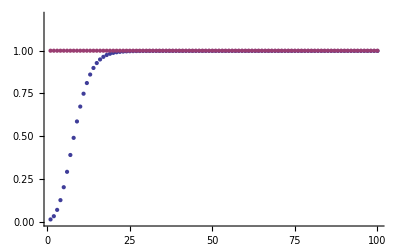

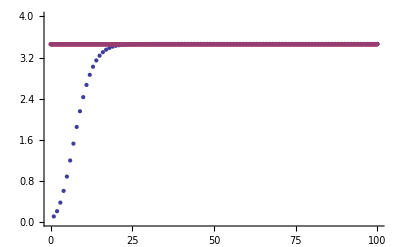

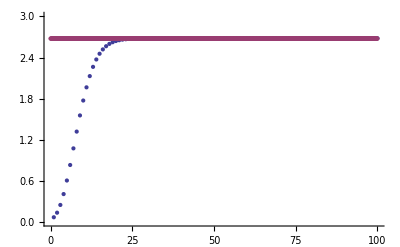

```mathematica
ListPlot[{Dn,De}, PlotRange-> {0,1.2}]
ListPlot[{RR,RE},PlotRange->{0,4}]
ListPlot[{ZZ,ZE},PlotRange->{0,3}]
```

-Graphics3D-

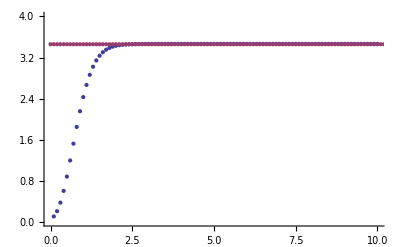

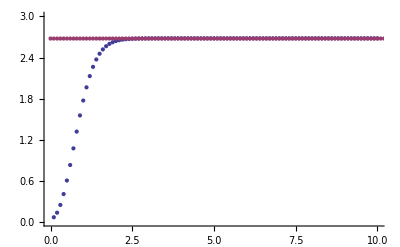

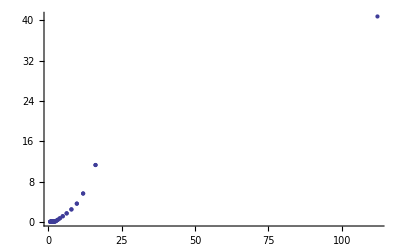

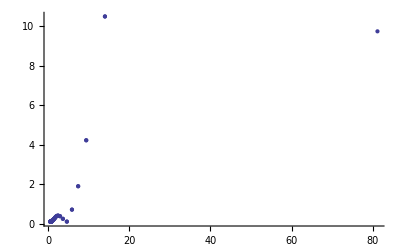

```mathematica
ListPointPlot3D[Transpose[{tt,Dz,Dr}]]
ListPlot[{Transpose[{tt,√Dr}],RE},PlotRange->{{0,10},{0,4}}]
ListPlot[{Transpose[{tt,√Dz}],ZE},PlotRange->{{0,10},{0,3}}]
ListPlot[Abs[Fourier[Transpose[{tt,Dr}]]]]
ListPlot[Abs[Fourier[Transpose[{tt,Dz}]]]]
```

### Collective Excitations

#### By complite numérical inital conditions

Here we are using the before numérical solutions, which comes from a simulations of the ground state with λ=0.9, as initial conditions for a simulation in other anisotropy (λ=0.8).

```mathematica
Import["/Users/rafael/xmds/rza-oscilation/vortex-ce-p.h5",{"Datasets"}]
```

{/1/Dr,/1/t,/2/Dz,/2/t}

```mathematica
Dr=Import["/Users/rafael/xmds/rza-oscilation/vortex-ce-p.h5",{"Datasets","/1/Dr"}];
Dz=Import["/Users/rafael/xmds/rza-oscilation/vortex-ce-p.h5",{"Datasets","/2/Dz"}];
Dn=Import["/Users/rafael/xmds/rza-oscilation/vortex-ce-p.h5",{"Datasets","/3/Dn"}];
tt=Import["/Users/rafael/xmds/rza-oscilation/vortex-ce-p.h5",{"Datasets","/1/t"}];
```

```mathematica
NN=Table[{tt[[i]],Dn[[i]]},{i,Dimensions[tt][[1]]}];
ZZ=Table[{tt[[i]],√Dz[[i]]},{i,Dimensions[tt][[1]]}];
RR=Table[{tt[[i]],√Dr[[i]]},{i,Dimensions[tt][[1]]}];
```

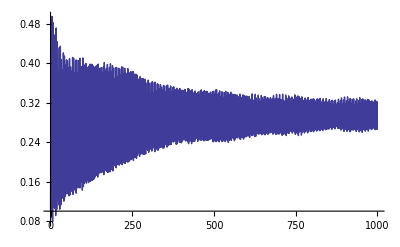

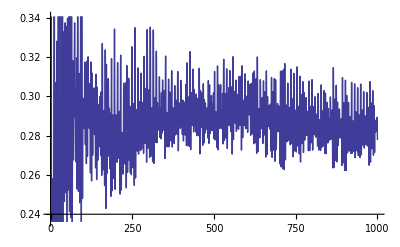

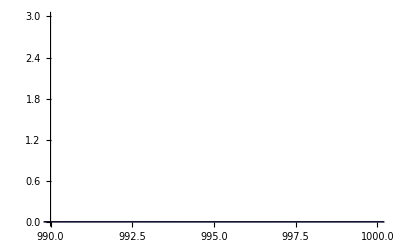

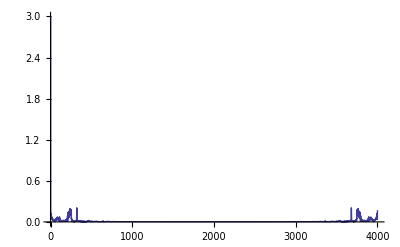

```mathematica
ListLinePlot[{Transpose[{tt,√Dr}]}]
ListLinePlot[{Transpose[{tt,√Dz}]}]
ListLinePlot[Abs[Fourier[√Dr]],PlotRange->{{990,1000},{0,3}}]
ListLinePlot[Abs[Fourier[√Dz]],PlotRange->{0,3}]
```

```mathematica
Print["ω_2=",ω1=1.421];Print["ω_2=",ω2=2.231];Print["ω_3=",ω3=9.062]
Print["ω_3 - 2 ω_1=",ω3-2ω1]

Print["Frequencies from graphic"]
Print["ν_1=",ν1=N[(2π)/1000]*99];Print["ν_2=",ν2=N[(2π)/1000]*235];Print["ν_3=",ν3=N[(2π)/1000]*332];Print["ν_4=",ν4=N[(2π)/1000]*664];Print["ν_5=",ν5=N[(2π)/1000]*995]
Print["2ν_3=ν_4=",2ν3]


Print["ratio"]
Print["ν_2/ω_1=",ν2/ω1]
Print["ν_3/ω_2=",ν3/ω2]
Print["ν_5/ω_3=",ν5/(ω3-2ω1)]
ClearAll[ω1,ω2,ω3,ν1,ν2,ν3,ν4,ν5]
```

ω_2=1.421

ω_2=2.231

ω_3=9.062

ω_3 - 2 ω_1=6.22

Frequencies from graphic

ν_1=0.622035

ν_2=1.47655

ν_3=2.08602

ν_4=4.17204

ν_5=6.25177

2ν_3=ν_4=4.17204

ratio

ν_2/ω_1=1.03909

ν_3/ω_2=0.935015

ν_5/ω_3=1.00511

#### By TF Ansatz

Initial conditions through the TF-Ansatz where the parameter was calculated semi-analiticaly for an anisotropia λ=0.9. The simulations was used the same value of λ. Once the Ansatz has a little difference than the numérical simulation of 0.1%, it can be used to obtain the frequencies of collective modes.

```mathematica
Import["/Users/rafael/xmds/rza-oscilation/vortex-ce-TF.h5",{"Datasets"}]
```

{/1/Dr,/1/t,/2/Dz,/2/t}

```mathematica
Dr=Import["/Users/rafael/xmds/rza-oscilation/vortex-ce-TF.h5",{"Datasets","/1/Dr"}];
Dz=Import["/Users/rafael/xmds/rza-oscilation/vortex-ce-TF.h5",{"Datasets","/2/Dz"}];
tt=Import["/Users/rafael/xmds/rza-oscilation/vortex-ce-TF.h5",{"Datasets","/1/t"}];
```

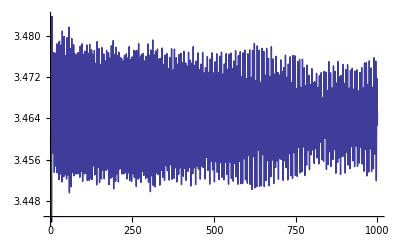

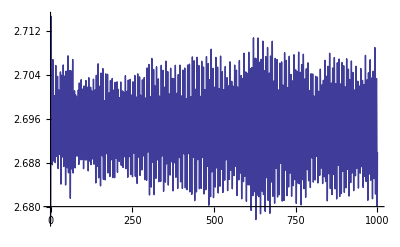

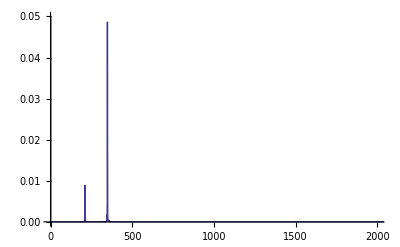

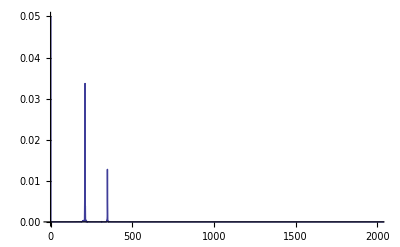

```mathematica
ListLinePlot[Transpose[{tt,√Dr}]]
ListLinePlot[Transpose[{tt,√Dz}]]
ListLinePlot[Abs[Fourier[√Dr]]^2,PlotRange->{{0,2000},{0,0.05}}]
ListLinePlot[Abs[Fourier[√Dz]]^2,PlotRange->{{0,2000},{0,0.05}}]
```

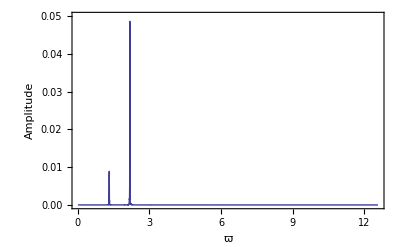

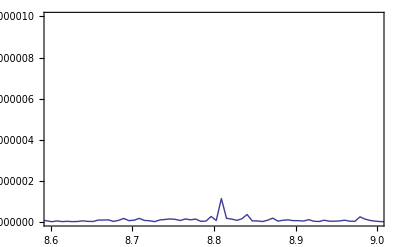

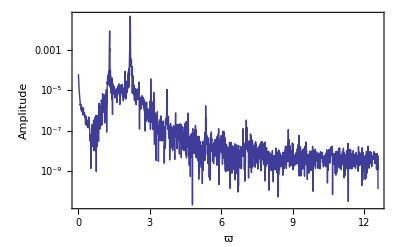

```mathematica
DrF=Abs[Fourier[√Dr]]^2;
ListPlot[Table[{i((2π)/1000),DrF[[i]]},{i,3,2000}],PlotRange->{0,0.05},Frame->True,Axes->False,Joined->True,FrameLabel->{"ϖ","Amplitude"},LabelStyle->{Medium}]
ListPlot[Table[{i((2π)/1000),DrF[[i]]},{i,0,2000}],PlotRange->{{8.6,9},{0,0.000001}},Frame->True,Axes->False,Joined->True,LabelStyle->{Medium}]
ListLogPlot[Table[{i((2π)/1000),DrF[[i]]},{i,3,2000}],PlotRange->All,Frame->True,Axes->False,Joined->True,FrameLabel->{"ϖ","Amplitude"},LabelStyle->{Medium}]
```

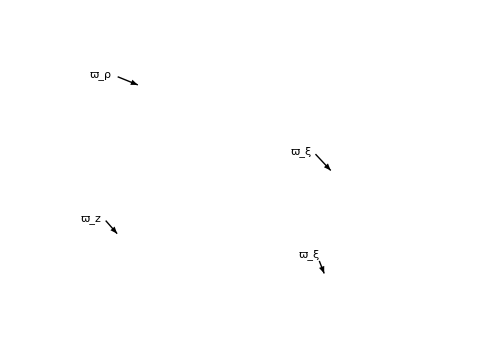
```mathematica
Export["nfline.eps",-Graphics-]
```

nfline.eps

```mathematica
(N[(2π)/1000]211)/1.317
(N[(2π)/1000]348)/2.166
(N[(2π)/1000]1412)/8.874
```

1.00665

1.00949

0.999759

0.994363

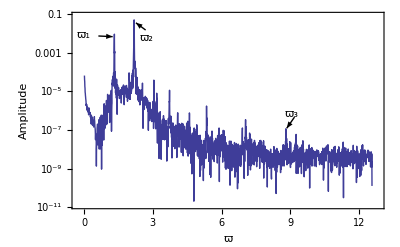
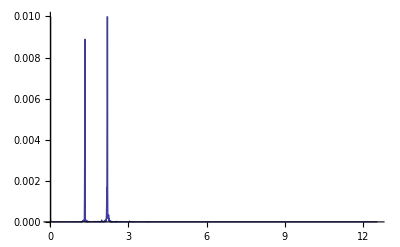
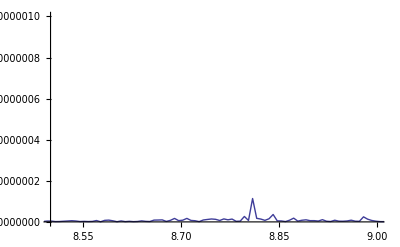
```mathematica
Export["nf.eps",-Graphics-]
Export["nfl.eps",-Graphics-]
Export["nfz.eps",-Graphics-]
```

nf.eps

nfl.eps

nfz.eps

### Scattering lenght modulation

```mathematica
Import["/Users/rafael/xmds/rza-oscilation/vortex-ce-asTF.h5",{"Datasets"}]
```

{/1/Dr,/1/t,/2/Dz,/2/t}

```mathematica
Dr=Import["/Users/rafael/xmds/rza-oscilation/vortex-ce-asTf.h5",{"Datasets","/1/Dr"}];
Dz=Import["/Users/rafael/xmds/rza-oscilation/vortex-ce-asTF.h5",{"Datasets","/2/Dz"}];
tt=Import["/Users/rafael/xmds/rza-oscilation/vortex-ce-asTF.h5",{"Datasets","/1/t"}];
```

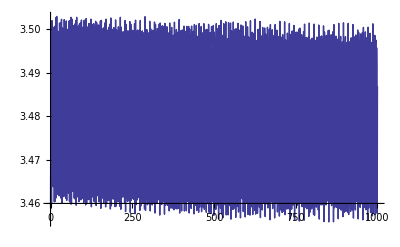

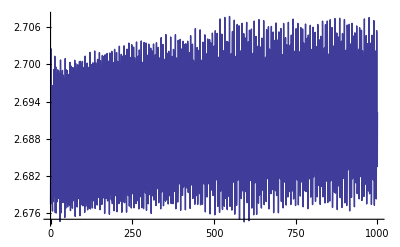

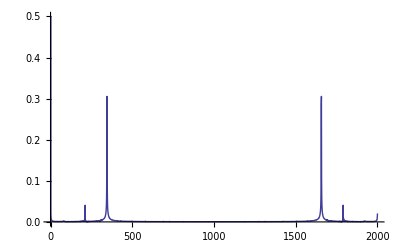

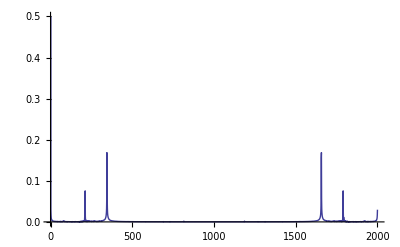

```mathematica
ListLinePlot[Transpose[{tt,√Dr}]]
ListLinePlot[Transpose[{tt,√Dz}]]
ListLinePlot[Abs[Fourier[√Dr]],PlotRange->{0,0.5}]
ListLinePlot[Abs[Fourier[√Dz]],PlotRange->{0,0.5}]
```

```mathematica
N[(2π)/1000]
N[(2π)/1000]
N[(2π)/1000]
```

## Vortex charge ℓ=2

### Imaginary time evolution

A anisotropia do sistema é de λ=0.4.

```mathematica
Import["/Users/rafael/xmds/rza-oscilation/l2-vortex-ce-i.h5",{"Datasets"}]
```

{/1/Dr,/1/t,/2/Dz,/2/t,/3/Dn,/3/t}

```mathematica
Dr=Import["/Users/rafael/xmds/rza-oscilation/l2-vortex-ce-i.h5",{"Datasets","/1/Dr"}];
Dz=Import["/Users/rafael/xmds/rza-oscilation/l2-vortex-ce-i.h5",{"Datasets","/2/Dz"}];
Dn=Import["/Users/rafael/xmds/rza-oscilation/l2-vortex-ce-i.h5",{"Datasets","/3/Dn"}];
tt=Import["/Users/rafael/xmds/rza-oscilation/l2-vortex-ce-i.h5",{"Datasets","/1/t"}];
```

```mathematica
ZZ=Table[√Dz[[i]],{i,Dimensions[Dz][[1]]}];
RR=Table[√Dr[[i]],{i,Dimensions[Dr][[1]]}];
De=Table[{i,1},{i,1,100,1}];
RE=Table[{i,2.44105},{i,0,100,0.1}];
ZE=Table[{i,14.9468},{i,0,100,0.1}];
```

```mathematica
Dn[[100]]
ZZ[[100]]
RR[[100]]
ZZ[[100]]/14.9468
RR[[100]]/2.44105
```

1.0029

14.8489

2.47774

0.993448

1.01503

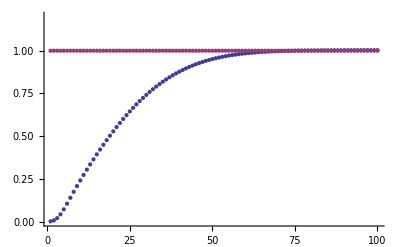

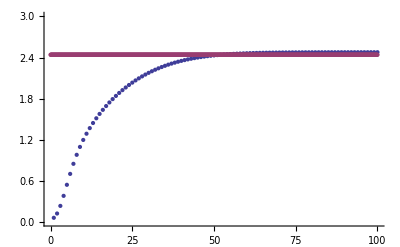

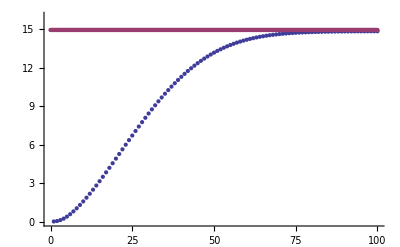

```mathematica
ListPlot[{Dn,De}, PlotRange-> {0,1.2}]
ListPlot[{RR,RE},PlotRange->{0,3}]
ListPlot[{ZZ,ZE},PlotRange->{0,16}]
```

-Graphics3D-

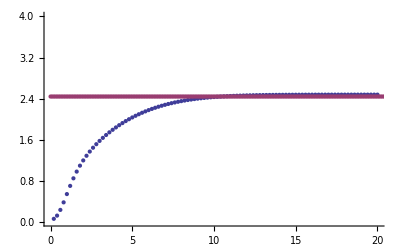

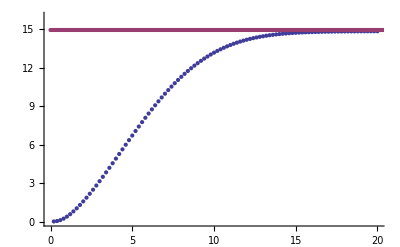

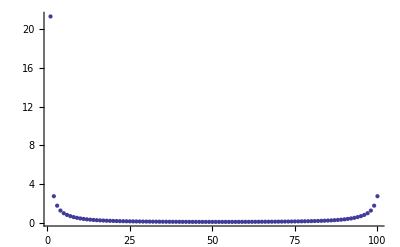

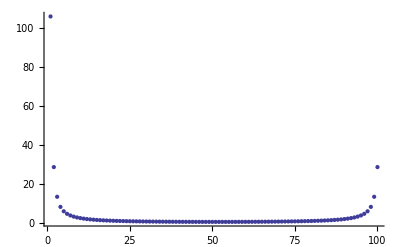

```mathematica
ListPointPlot3D[Transpose[{tt,Dz,Dr}]]
ListPlot[{Transpose[{tt,√Dr}],RE},PlotRange->{{0,20},{0,4}}]
ListPlot[{Transpose[{tt,√Dz}],ZE},PlotRange->{{0,20},{0,16}}]
ListPlot[Abs[Fourier[√Dr]]]
ListPlot[Abs[Fourier[√Dz]]]
```

### Collective excitations by TF Ansatz

Initial conditions through the TF-Ansatz where the parameter was calculated semi-analiticaly for an anisotropia λ=0.4. The simulations was used the same value of λ. Once the Ansatz has a little difference than the numérical simulation of 0.1%, it can be used to obtain the frequencies of collective modes.

```mathematica
Import["/Users/rafael/xmds/rza-oscilation/l2-vortex-ce-TF.h5",{"Datasets"}]
```

{/1/Dr,/1/t,/2/Dz,/2/t}

```mathematica
Dr=Import["/Users/rafael/xmds/rza-oscilation/l2-vortex-ce-TF.h5",{"Datasets","/1/Dr"}];
Dz=Import["/Users/rafael/xmds/rza-oscilation/l2-vortex-ce-TF.h5",{"Datasets","/2/Dz"}];
tt=Import["/Users/rafael/xmds/rza-oscilation/l2-vortex-ce-TF.h5",{"Datasets","/1/t"}];
```

```mathematica
ZZ=Table[√Dz[[i]],{i,Dimensions[Dz][[1]]}];
RR=Table[√Dr[[i]],{i,Dimensions[Dr][[1]]}];
De=Table[{i,1},{i,1,100,1}];
```

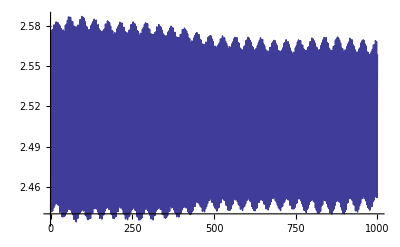

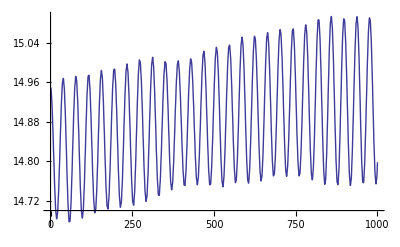

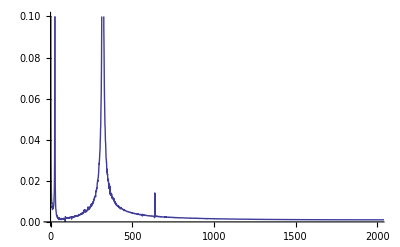

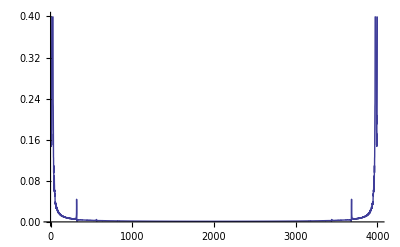

```mathematica
ListLinePlot[Transpose[{tt,√Dr}]]
ListLinePlot[Transpose[{tt,√Dz}]]
ListLinePlot[Abs[Fourier[√Dr]],PlotRange->{{0,2000},{0,0.1}}]
ListLinePlot[Abs[Fourier[√Dz]],PlotRange->{0,0.4}]
```

```mathematica
(N[(2π)/1000]102)/0.632
(N[(2π)/1000]332)/2.019
N[(2π)/1000]^-1 6.053
```

1.01406

1.03319

963.365